## Figure of Fussmann Data

## Setup

```mathematica
(* Set Directory *)
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_16/hopf_fussmann_2000"];
```

```mathematica
(* get package for user-defined functions *)
Get["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Mathematica/packages/my_functions/spectral_functions.wl"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};

(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

## Import .mat data file

```mathematica
dataSet=Import["data_export/seriesData.mat"];
```

## Entire time-series plot

```mathematica
(* plot parameters *)
padding={{50,50},{50,30}};
tmax=130;
```

```mathematica
dataSet//Dimensions
```

{14}

```mathematica
(* Plot of prey (chlorella) *)
Clear[plotChlorella]
plotChlorella[i_]:=ListLinePlot[dataSet[[i,;;,{1,2}]],
Joined->True,
LabelStyle->14,
FrameLabel->{{"Chlorella (10^6 cells/ml)","Brachionus (females/ml)"},{"Time",""}},
Frame->{{True,False},{True,True}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->300,
PlotStyle->{TMBcolours[[1]]},
PlotRange->{{0,tmax},{0,5}},
Epilog->Text[Style["δ= "<>ToString[AccountingForm[deltaVals[[i]],{3,2}]],14],Scaled[{0.15,1.1}]],
PlotRangeClipping->False,
ImageSize->400];
```

```mathematica
(* Plot of predator (brachionus) *)
Clear[plotBrachionus]
plotBrachionus[i_]:=ListLinePlot[dataSet[[i,;;,{1,3}]],
Joined->True,
LabelStyle->14,
FrameLabel->{{"","Brachionus (females/ml)"},{"Time",""}},
Frame->{{False,True},{True,True}},
FrameTicks->{{None,Range[0,45,10]},{Automatic,None}},
FrameStyle->{{Automatic,TMBcolours[[2]]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->300,
PlotStyle->{TMBcolours[[2]]},
PlotRange->{{0,tmax},{0,40}}];
```

```mathematica
(* overlay the plots *)
Clear[joinPlot]
joinPlot[i_]:=Overlay[{plotChlorella[i],plotBrachionus[i]}]
```

```mathematica
Partition[Range[1,14],3]
```

{{1,2,3},{4,5,6},{7,8,9},{10,11,12}}

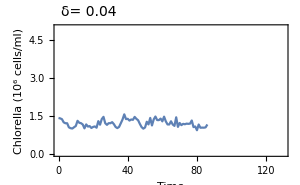
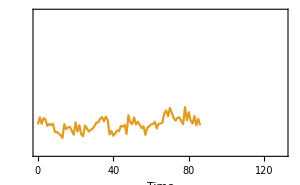
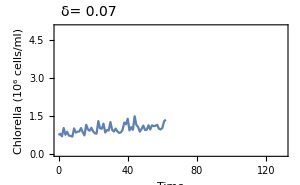
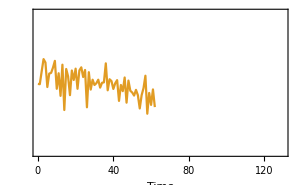
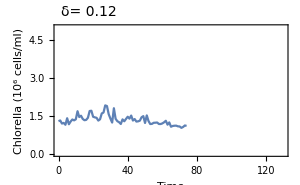
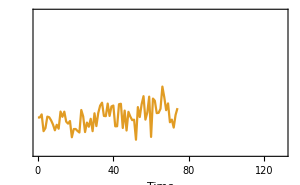
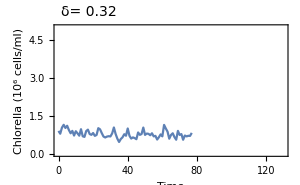
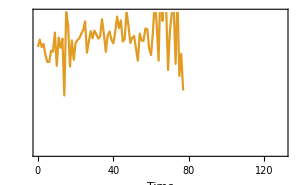
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- |

```mathematica
(* Display plots *)
plotDataFussmann=Grid[Partition[Table[joinPlot[i],{i,1,Length[deltaVals]}],UpTo[3]]]
```

## Statistical Indicators

### Parameters

```mathematica
bandWidth=20; (* number of days *)
hamLength=40;
hamOffset=20;
```

```mathematica
(* make arrays to store metrics *)
fitPlotChlor=ConstantArray[0,Length[deltaVals]];
varChlor=ConstantArray[0,Length[deltaVals]];
cvarChlor=ConstantArray[0,Length[deltaVals]];
acChlor=ConstantArray[0,Length[deltaVals]];
psChlor=ConstantArray[0,Length[deltaVals]];
aicFoldChlor=ConstantArray[0,Length[deltaVals]];
aicHopfChlor=ConstantArray[0,Length[deltaVals]];
smaxChlor=ConstantArray[0,Length[deltaVals]];
cfChlor=ConstantArray[0,Length[deltaVals]];
lenChlor=ConstantArray[0,Length[deltaVals]];


fitPlotBrach=ConstantArray[0,Length[deltaVals]];
varBrach=ConstantArray[0,Length[deltaVals]];
cvarBrach=ConstantArray[0,Length[deltaVals]];
acBrach=ConstantArray[0,Length[deltaVals]];
psBrach=ConstantArray[0,Length[deltaVals]];
aicFoldBrach=ConstantArray[0,Length[deltaVals]];
aicHopfBrach=ConstantArray[0,Length[deltaVals]];
smaxBrach=ConstantArray[0,Length[deltaVals]];
cfBrach=ConstantArray[0,Length[deltaVals]];
lenBrach=ConstantArray[0,Length[deltaVals]];

(* array for psd plots *)
psPlots=ConstantArray[0,Length[deltaVals]];
```

### Function to detrend and compute EWS

```mathematica
Clear[ews]
ews[bandWidth_,yVals_,tVals_]:=
Module[{dataFit,len,dt,residuals,variance,mean,cvar,autoCorr,pSpec,aicFold,aicHopf,aicNull,smax,coherFactor,plot,output},
len=Length[yVals];
dt=tVals[[2]]-tVals[[1]];
(* Detrend t-series using Gaussian filtering - no filtering if bandwidth is zero, no filtering *)
If[bandWidth≠0,
dataFit=GaussianFilter[yVals,bandWidth];,
dataFit=ConstantArray[0,Length[yVals]];
];
(* make a plot *)
plot=ListLinePlot[{Transpose[{tVals,yVals}],Transpose[{tVals,dataFit}]},
ImageSize->250,
Frame->True,
LabelStyle->12,
FrameLabel->{{"Abundance",None},{"Time",None}},
PlotRange->All];
(* Find residual dynamics *);
residuals=yVals-dataFit;
(* Compute variance indicator *)
variance=Variance[residuals];
(* Compute mean of series *)
mean=Mean[yVals];
(* Compute coefficient of variation *)
cvar=variance/mean;
(* Compute lag-1 autocorrelation *)
autoCorr=CorrelationFunction[residuals,1];
(* Compute power spectrum *)
pSpec=TBPowerSpecWelch[{residuals,dt,hamLength,hamOffset}];
(* Compute AIC weight *)
{aicFold,aicHopf,aicNull}=TBFitSpec[pSpec];
(* Compute smax *)
smax=Max[pSpec[[2,;;]]];
(* Compute coherence factor *)
coherFactor=TBCoherFactor[pSpec];
(* Output *)
output={len,plot,variance,cvar,autoCorr,pSpec,aicFold,aicHopf,smax,coherFactor}
]
```

```mathematica
?TBFitSpec
```

TBFitSpec[pSpec] fits three power spectrum models to the input: unimodal, bimodal and flat (null).
pSpec = {freqVals,powerVals}
Outputs {foldWeight, hopfWeight, nullWeight}
AIC weights can be interpreted as the probability that the fitted model is the best model (in the AIC sense);

```mathematica
?TBPowerSpecWelch
```

{freqVals,pSpec} = TBPowerSpecWelch[{yVals,dt,hamLength,hamOffset}] estimates the power spectrum usign Welch's method.
This involves computing the periodogram with overlapping Hamming windows.
hamLength: number of data points in Hamming window, or if in (0,1) taken as a proportion of total data input
hamOffset: number of data points to offset the window by on each interation, or if in (0,1) taken as a proportion of Hamming window size

### Function to plot PS and display EWS data

```mathematica
Clear[psPlot]
psPlot[i_,ωmax_]:=Grid[{{
ListLinePlot[Transpose[psChlor[[i]]],
PlotRange->{{-ωmax,ωmax},All},
Filling->Bottom,
AxesLabel->{"ω","S_chlor(ω)"},
LabelStyle->12,
ImageSize->300,
AspectRatio->1/2,
Epilog->{Text[Style["δ= "<>ToString[NumberForm[deltaVals[[i]],{3,2}]],12,Bold],Scaled[{0,0.95}],Left],
Text[Style["T= "<>ToString[lenChlor[[i]]],12],Scaled[{0,0.85}],Left],
Text[Style["Var= "<>ToString[NumberForm[varChlor[[i]],{3,2}]],12],Scaled[{1,0.95}],Right],
Text[Style["CV= "<>ToString[NumberForm[cvarChlor[[i]],{3,2}]],12],Scaled[{1,0.85}],Right],
Text[Style["AC= "<>ToString[NumberForm[acChlor[[i]],{3,2}]],12],Scaled[{1,0.75}],Right],Text[Style["w_fold= "<>ToString[AccountingForm[NumberForm[aicFoldChlor[[i]],{3,2}]]],12],Scaled[{1,0.65}],Right],
Text[Style["w_hopf= "<>ToString[AccountingForm[NumberForm[aicHopfChlor[[i]],{3,2}]]],12],Scaled[{1,0.55}],Right],
Text[Style["S_max= "<>ToString[NumberForm[smaxChlor[[i]],{3,2}]],12],Scaled[{1,0.45}],Right],
Text[Style["CF= "<>ToString[NumberForm[cfChlor[[i]],{3,2}]],12],Scaled[{1,0.35}],Right]}
]},
{ListLinePlot[Transpose[psBrach[[i]]],
PlotRange->{{-ωmax,ωmax},All},
Filling->Bottom,
AxesLabel->{"ω","S_brach(ω)"},
LabelStyle->12,
ImageSize->300,
AspectRatio->1/2,
Epilog->{Text[Style["δ= "<>ToString[NumberForm[deltaVals[[i]],{3,2}]],12,Bold],Scaled[{0,0.95}],Left],
Text[Style["T= "<>ToString[lenBrach[[i]]],12],Scaled[{0,0.85}],Left],
Text[Style["Var= "<>ToString[NumberForm[varBrach[[i]],{3,2}]],12],Scaled[{1,0.95}],Right],
Text[Style["CV= "<>ToString[NumberForm[cvarBrach[[i]],{3,2}]],12],Scaled[{1,0.85}],Right],
Text[Style["AC= "<>ToString[NumberForm[acBrach[[i]],{3,2}]],12],Scaled[{1,0.75}],Right],
Text[Style["w_fold= "<>ToString[AccountingForm[NumberForm[aicFoldBrach[[i]],{3,2}]]],12],Scaled[{1,0.65}],Right],
Text[Style["w_hopf= "<>ToString[AccountingForm[NumberForm[aicHopfBrach[[i]],{3,2}]]],12],Scaled[{1,0.55}],Right],
Text[Style["S_max= "<>ToString[NumberForm[smaxBrach[[i]],{3,2}]],12],Scaled[{1,0.45}],Right],
Text[Style["CF= "<>ToString[NumberForm[cfBrach[[i]],{3,2}]],12],Scaled[{1,0.35}],Right]}
]}}
,Spacings->{-2,-0.5}]
```

### Playground

```mathematica
(*ListLinePlot[dataSet[[dNum,;;,2]],PlotRange->All]*)
```

```mathematica
(*PeriodogramArray[dataSet[[dNum,;;,2]]];*)
```

```mathematica
(*Periodogram[dataSet[[dNum,;;,2]],PlotRange->All]*)
```

```mathematica
(*pSpec=TBPowerSpec[{dataSet[[dNum,;;,2]],1}];*)
```

```mathematica
(*ListLinePlot[Transpose[pSpec]]*)
```

### δ=1.37

```mathematica
dNum=14;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

$Aborted

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

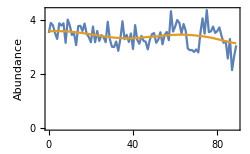
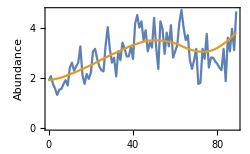

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.126811,0.349431}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.0371762,0.120319}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.232286,0.262365}

```mathematica
(* fold weights *)
{aicFoldChlor[[dNum]],aicFoldBrach[[dNum]]}
```

{0.409665,0.99971}

```mathematica
(* hopf weights *)
{aicHopfChlor[[dNum]],aicHopfBrach[[dNum]]}
```

{1.10475×10^-6,0.0000897766}

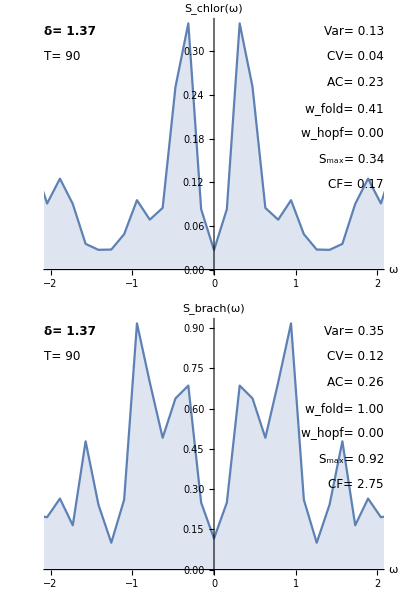

```mathematica
(* power spectra *)
wmax=2;
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=1.24

```mathematica
dNum=13;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

NonlinearModelFit::lmnl: The model myFunctions`Private`c is linear in the parameters {myFunctions`Private`c}, but a nonlinear method or non-Euclidean norm was specified, so nonlinear methods will be used.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partd: Part specification Optimization`NMinimizeDump`best⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {Optimization`NMinimizeDump`best⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Floor[1/2 (1+Sign[-0.001+Abs[Part[«2»]]])]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part {2,1,2,1} of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {Optimization`NMinimizeDump`best⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads Equal and LessEqual at positions 1 and 2 are expected to be the same.

NMinimize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: Join[{}⟦{2,1,2,1}⟧==0,{}⟦{2,1,2,1}⟧≤0].

Part::partd: Part specification Optimization`NMinimizeDump`best⟦1⟧ is longer than depth of object.

Set::partd: Part specification Optimization`NMinimizeDump`result⟦1⟧ is longer than depth of object.

Part::partd: Part specification Optimization`NMinimizeDump`best⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Set::partd: Part specification Optimization`NMinimizeDump`result⟦2⟧ is longer than depth of object.

Join::heads: Heads Equal and LessEqual at positions 1 and 2 are expected to be the same.

NMinimize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: Join[{}⟦{2,1,2,1}⟧==0,{}⟦{2,1,2,1}⟧≤0].

Set::partd: Part specification Optimization`NMinimizeDump`result⟦1⟧ is longer than depth of object.

General::stop: Further output of Set::partd will be suppressed during this calculation.

Join::heads: Heads Equal and LessEqual at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

NMinimize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: Join[{}⟦{2,1,2,1}⟧==0,{}⟦{2,1,2,1}⟧≤0].

General::stop: Further output of NMinimize::nosat will be suppressed during this calculation.

NonlinearModelFit::lmnl: The model myFunctions`Private`c is linear in the parameters {myFunctions`Private`c}, but a nonlinear method or non-Euclidean norm was specified, so nonlinear methods will be used.

$Aborted

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

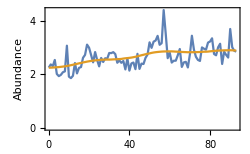
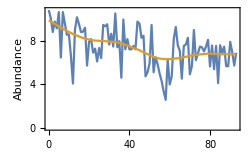

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.127301,2.321}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.0479087,0.313762}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.403734,0.0993625}

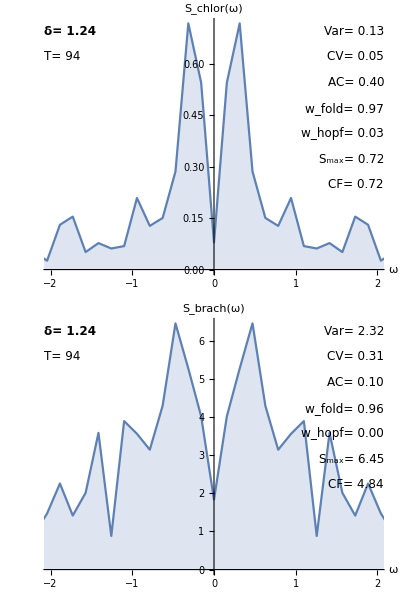

```mathematica
(* power spectra *)
wmax=2;
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=1.17

```mathematica
dNum=12;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

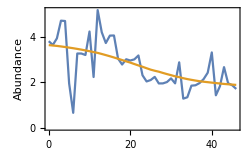
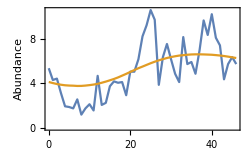

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.614376,3.51672}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.226249,0.674292}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.237771,0.5472}

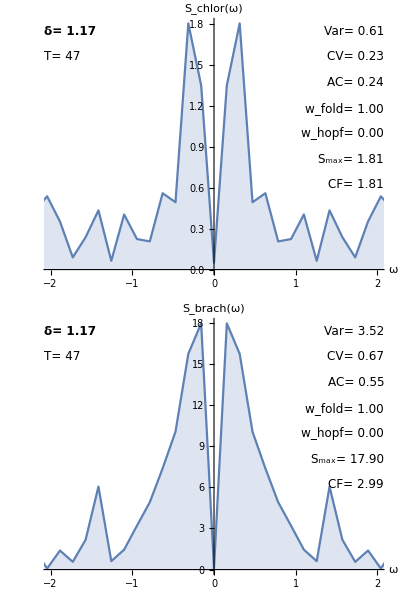

```mathematica
(* power spectra *)
wmax=2;
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=1.15

```mathematica
dNum=11;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

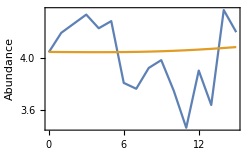
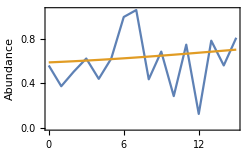

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.0751494,0.0613103}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.0187376,0.10171}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.428347,-0.123633}

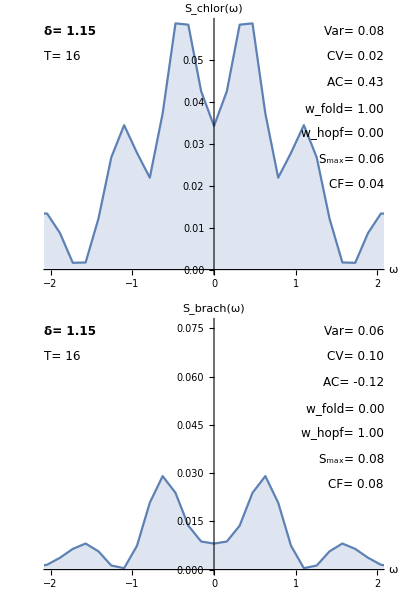

```mathematica
(* power spectra *)
wmax=2;
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=1.00

```mathematica
dNum=10;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

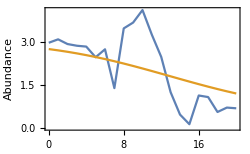
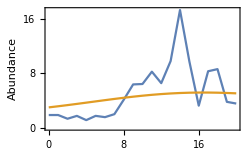

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.852393,13.1396}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.402072,2.52098}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.653475,0.545623}

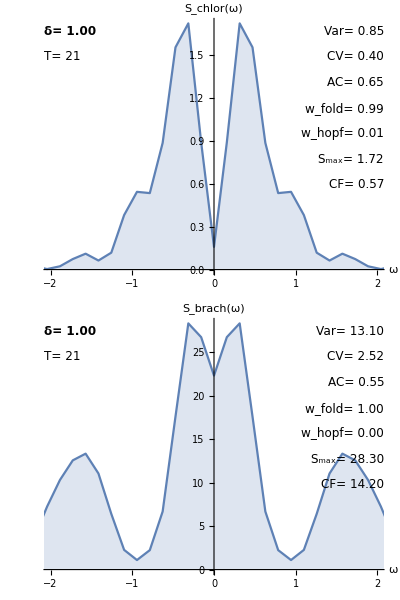

```mathematica
(* power spectra *)
wmax=2;
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=0.95

```mathematica
dNum=9;
plot=joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

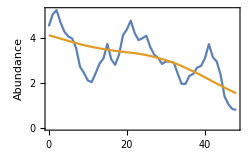
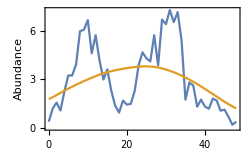

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.585863,3.19585}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.188684,1.0146}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.847593,0.787201}

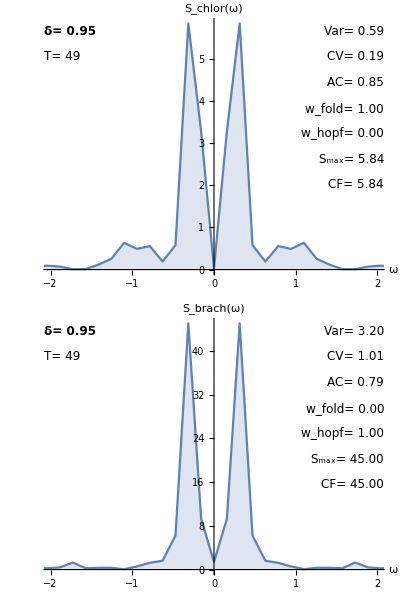

```mathematica
(* power spectra *)
wmax=2;
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=0.89

```mathematica
dNum=8;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

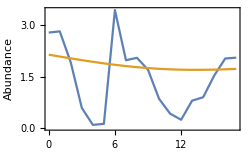
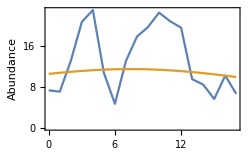

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.943747,37.8228}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.646156,2.83288}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.39112,0.536696}

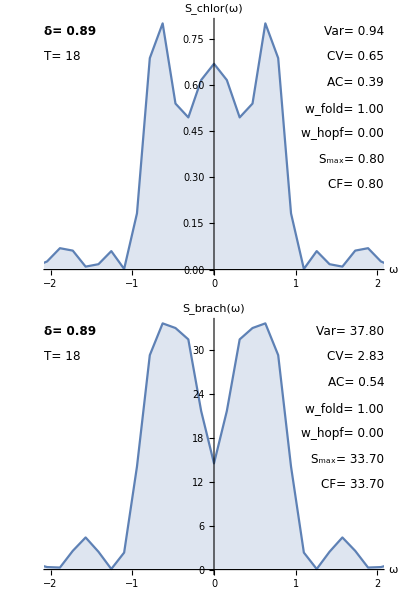

```mathematica
(* power spectra *)
wmax=2;
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=0.69

```mathematica
dNum=7;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

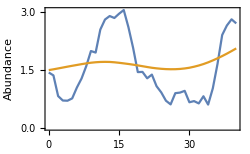
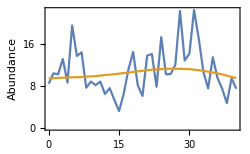

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.562227,18.2924}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.362727,1.68792}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.911204,0.302492}

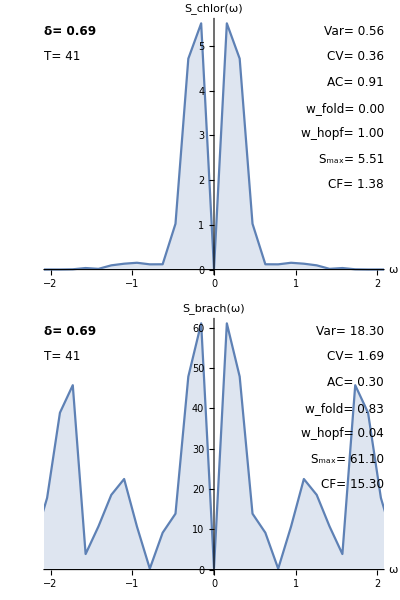

```mathematica
(* power spectra *)
wmax=2;
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=0.67

```mathematica
dNum=6;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

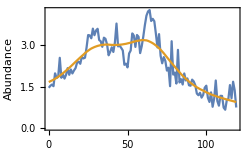
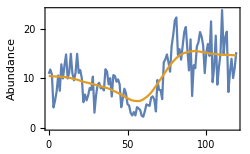

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.159309,10.6625}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.0693849,0.99953}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.481751,0.313848}

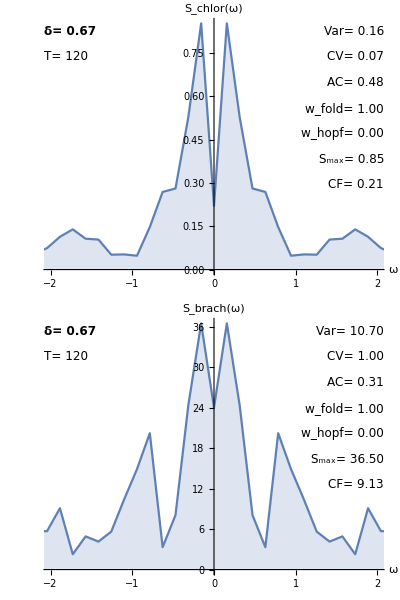

```mathematica
(* power spectra *)
wmax=2;
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=0.64

```mathematica
dNum=5;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

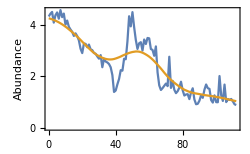
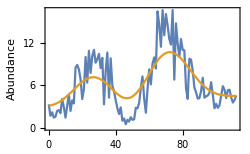

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.202879,6.20184}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.0823051,0.987784}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.695711,0.424995}

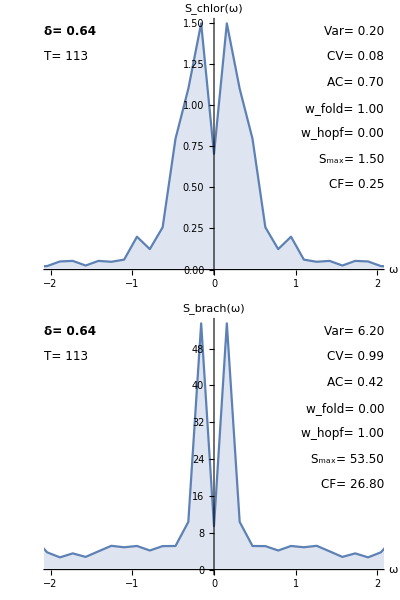

```mathematica
(* power spectra *)
wmax=2;
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=0.32

```mathematica
dNum=4;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

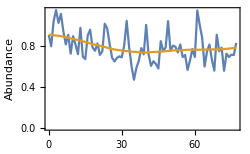
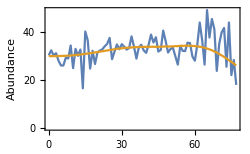

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.0174318,28.3647}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.0222971,0.8703}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.275546,-0.0485641}

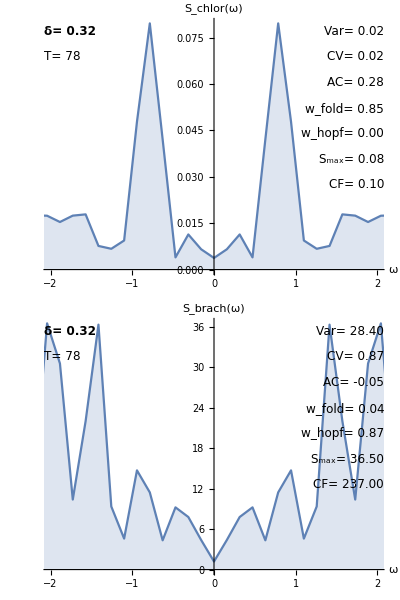

```mathematica
(* power spectra *)
wmax=2;
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=0.12

```mathematica
dNum=3;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

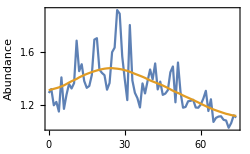
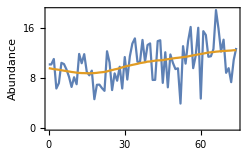

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.0180072,7.74683}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.0134985,0.749026}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.340764,0.04364}

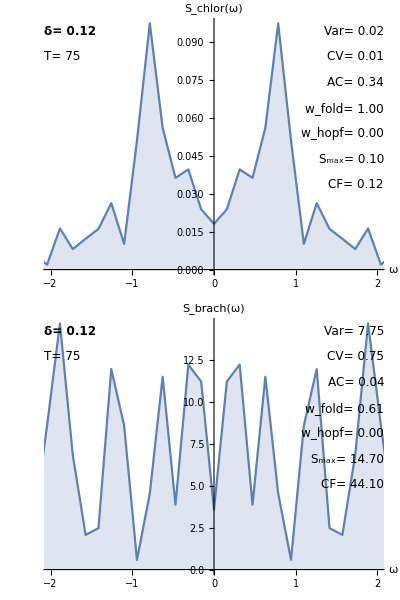

```mathematica
(* power spectra *)
wmax=2;
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=0.07

```mathematica
dNum=2;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

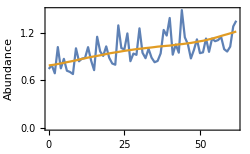
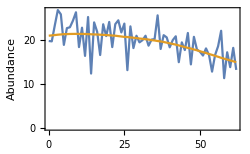

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.0213872,9.20274}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.0217562,0.467076}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.0403634,-0.364912}

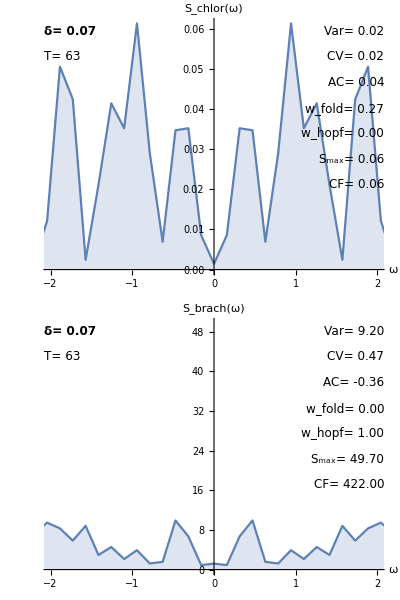

```mathematica
(* power spectra *)
wmax=2;
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=0.04

```mathematica
dNum=1;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

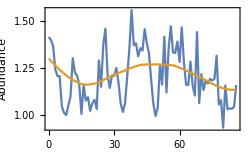
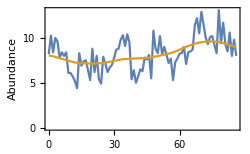

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.0155251,2.27817}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.0128837,0.276764}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.429172,0.323209}

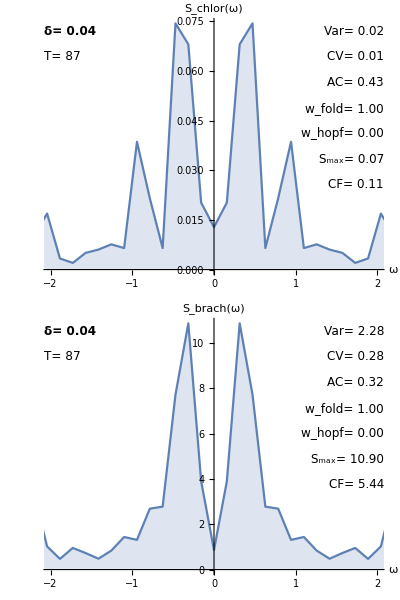

```mathematica
(* power spectra *)
wmax=2;
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### Plot of EWS statistics

```mathematica
ewsFramePlot=Grid[Partition[Table[psPlots[[i]],{i,1,Length[deltaVals]}],UpTo[3]],Spacings->{3,1},Frame->All]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
(*Export["figures/fussmann_ews_summary.png",ewsFramePlot,ImageResolution->200];*)
```

### Overall statistics

```mathematica
NumberForm[deltaVals,{5,2}]
```

{0.04,0.07,0.12,0.32,0.64,0.67,0.69,0.89,0.95,1.00,1.15,1.17,1.24,1.37}

```mathematica
deltaValsRound=Table[NumberForm[deltaVals[[i]],{5,2}],{i,1,Length[deltaVals]}];
```

```mathematica
labels={"delta vals","var Chlor","var Brach","cvar Chlor","cvar Brach","ac Chlor","ac Brach"};
```

```mathematica
labels//TableForm
```

delta vals
var Chlor
var Brach
cvar Chlor
cvar Brach
ac Chlor
ac Brach

```mathematica
{deltaValsRound,varChlor,varBrach,cvarChlor,cvarBrach,acChlor,acBrach}//TableForm
```

0.04 | 0.07 | 0.12 | 0.32 | 0.64 | 0.67 | 0.69 | 0.89 | 0.95 | 1.00 | 1.15 | 1.17 | 1.24 | 1.37
0.0155251 | 0.0213872 | 0.0180072 | 0.0174318 | 0.202879 | 0.159309 | 0.562227 | 0.943747 | 0.585863 | 0.852393 | 0.0751494 | 0.614376 | 0.127301 | 0.126811
2.27817 | 9.20274 | 7.74683 | 28.3647 | 6.20184 | 10.6625 | 18.2924 | 37.8228 | 3.19585 | 13.1396 | 0.0613103 | 3.51672 | 2.321 | 0.349431
0.0128837 | 0.0217562 | 0.0134985 | 0.0222971 | 0.0823051 | 0.0693849 | 0.362727 | 0.646156 | 0.188684 | 0.402072 | 0.0187376 | 0.226249 | 0.0479087 | 0.0371762
0.276764 | 0.467076 | 0.749026 | 0.8703 | 0.987784 | 0.99953 | 1.68792 | 2.83288 | 1.0146 | 2.52098 | 0.10171 | 0.674292 | 0.313762 | 0.120319
0.429172 | 0.0403634 | 0.340764 | 0.275546 | 0.695711 | 0.481751 | 0.911204 | 0.39112 | 0.847593 | 0.653475 | 0.428347 | 0.237771 | 0.403734 | 0.232286
0.323209 | -0.364912 | 0.04364 | -0.0485641 | 0.424995 | 0.313848 | 0.302492 | 0.536696 | 0.787201 | 0.545623 | -0.123633 | 0.5472 | 0.0993625 | 0.262365

```mathematica
varBrach
```

{2.27817,9.20274,7.74683,28.3647,6.20184,10.6625,18.2924,37.8228,3.19585,13.1396,0.0613103,3.51672,2.321,0.349431}

Paper Figure

```mathematica
(* figure numbers to include *)
figureNums={1,4,5,7,9,13,14};
aRatio=0.9;
imgSize=220;
labelPos={0.5,1.15};
padding={{50,50},{50,30}};
```

## Time-series figures

### figure 1

```mathematica
fig1Chlorella=ListLinePlot[dataSet[[1,;;,{1,2}]],
Joined->True,
LabelStyle->14,
FrameLabel->{{"Chlorella (10^6 cells/ml)","Brachionus (females/ml)"},{"Time",""}},
Frame->{{True,False},{True,True}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[1]]},
PlotRange->{{0,Max[dataSet[[1,;;,1]]]},{0,5}},
Epilog->Text[Style["δ= "<>ToString[AccountingForm[deltaVals[[1]],{3,2}]],14],Scaled[labelPos]],
PlotRangeClipping->False,
AspectRatio->aRatio];
```

```mathematica
(* Plot of predator (brachionus) *)
fig1Brach=ListLinePlot[dataSet[[1,;;,{1,3}]],
Joined->True,
LabelStyle->14,
FrameLabel->{{"",Style["Brachionus (females/ml)",White]},{"",""}},
Frame->{{False,True},{True,True}},
FrameTicks->{{None,None},{None,None}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[2]]},
PlotRange->{{0,Max[dataSet[[1,;;,1]]]},{0,50}},
AspectRatio->aRatio];
```

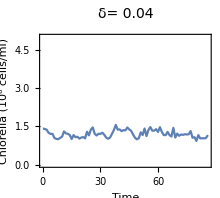
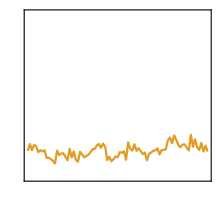

```mathematica
(* overlay the plots *)
fig1=Overlay[{fig1Chlorella,fig1Brach}]
```

### figure 2

```mathematica
fig2Chlorella=ListLinePlot[dataSet[[figureNums[[2]],;;,{1,2}]],
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],Style["Brachionus (females/ml)",White]},{"Time",""}},
Frame->{{True,False},{True,True}},
FrameTicks->{{None,None},{Range[0,80,20],None}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[1]]},
PlotRange->{{0,Max[dataSet[[figureNums[[2]],;;,1]]]},{0,5}},
Epilog->Text[Style["δ= "<>ToString[AccountingForm[deltaVals[[figureNums[[2]]]],{3,2}]],14],Scaled[labelPos]],
PlotRangeClipping->False,
AspectRatio->aRatio];
```

```mathematica
(* Plot of predator (brachionus) *)
fig2Brach=ListLinePlot[dataSet[[figureNums[[2]],;;,{1,3}]],
Joined->True,
LabelStyle->14,
FrameLabel->{{"",Style["Brachionus (females/ml)",White]},{"",""}},
Frame->{{False,True},{True,True}},
FrameTicks->{{None,None},{None,None}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[2]]},
PlotRange->{{0,Max[dataSet[[figureNums[[2]],;;,1]]]},{0,50}},
AspectRatio->aRatio];
```

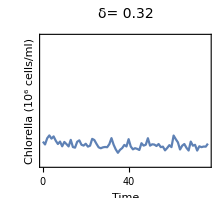
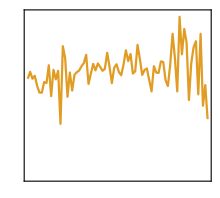

```mathematica
(* overlay the plots *)
fig2=Overlay[{fig2Chlorella,fig2Brach}]
```

### figure 3

```mathematica
fig3Chlorella=ListLinePlot[dataSet[[figureNums[[3]],;;,{1,2}]],
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],Style["Brachionus (females/ml)",White]},{"Time",""}},
Frame->{{True,False},{True,True}},
FrameTicks->{{None,None},{Range[0,100,20],None}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[1]]},
PlotRange->{{0,Max[dataSet[[figureNums[[3]],;;,1]]]},{0,5}},
Epilog->Text[Style["δ= "<>ToString[AccountingForm[deltaVals[[figureNums[[3]]]],{3,2}]],14],Scaled[labelPos]],
PlotRangeClipping->False,
AspectRatio->aRatio];
```

```mathematica
(* Plot of predator (brachionus) *)
fig3Brach=ListLinePlot[dataSet[[figureNums[[3]],;;,{1,3}]],
Joined->True,
LabelStyle->14,
FrameLabel->{{"",Style["Brachionus (females/ml)",White]},{"",""}},
Frame->{{False,True},{True,True}},
FrameTicks->{{None,None},{None,None}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[2]]},
PlotRange->{{0,Max[dataSet[[figureNums[[3]],;;,1]]]},{0,50}},
AspectRatio->aRatio];
```

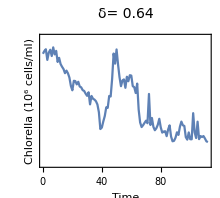
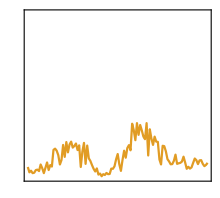

```mathematica
(* overlay the plots *)
fig3=Overlay[{fig3Chlorella,fig3Brach}]
```

### figure 4

```mathematica
fig4Chlorella=ListLinePlot[dataSet[[figureNums[[4]],;;,{1,2}]],
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],Style["Brachionus (females/ml)",White]},{"Time",""}},
Frame->{{True,False},{True,True}},
FrameTicks->{{None,None},{Range[0,100,20],None}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[1]]},
PlotRange->{{0,Max[dataSet[[figureNums[[4]],;;,1]]]},{0,5}},
Epilog->Text[Style["δ= "<>ToString[AccountingForm[deltaVals[[figureNums[[4]]]],{3,2}]],14],Scaled[labelPos]],
PlotRangeClipping->False,
AspectRatio->aRatio];
```

```mathematica
(* Plot of predator (brachionus) *)
fig4Brach=ListLinePlot[dataSet[[figureNums[[4]],;;,{1,3}]],
Joined->True,
LabelStyle->14,
FrameLabel->{{"",Style["Brachionus (females/ml)",White]},{"",""}},
Frame->{{False,True},{True,True}},
FrameTicks->{{None,None},{None,None}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[2]]},
PlotRange->{{0,Max[dataSet[[figureNums[[4]],;;,1]]]},{0,50}},
AspectRatio->aRatio];
```

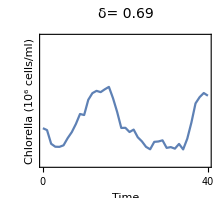
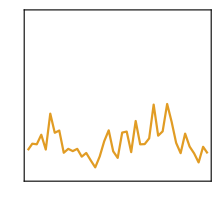

```mathematica
(* overlay the plots *)
fig4=Overlay[{fig4Chlorella,fig4Brach}]
```

### figure 5

```mathematica
fig5Chlorella=ListLinePlot[dataSet[[figureNums[[5]],;;,{1,2}]],
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],Style["Brachionus (females/ml)",White]},{"Time",""}},
Frame->{{True,False},{True,True}},
FrameTicks->{{None,None},{Range[0,100,20],None}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[1]]},
PlotRange->{{0,Max[dataSet[[figureNums[[5]],;;,1]]]},{0,5}},
Epilog->Text[Style["δ= "<>ToString[AccountingForm[deltaVals[[figureNums[[5]]]],{3,2}]],14],Scaled[labelPos]],
PlotRangeClipping->False,
AspectRatio->aRatio];
```

```mathematica
(* Plot of predator (brachionus) *)
fig5Brach=ListLinePlot[dataSet[[figureNums[[5]],;;,{1,3}]],
Joined->True,
LabelStyle->14,
FrameLabel->{{"",Style["Brachionus (females/ml)",White]},{"",""}},
Frame->{{False,True},{True,True}},
FrameTicks->{{None,None},{None,None}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[2]]},
PlotRange->{{0,Max[dataSet[[figureNums[[5]],;;,1]]]},{0,50}},
AspectRatio->aRatio];
```

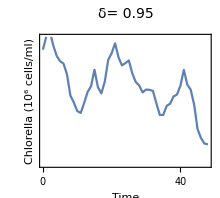
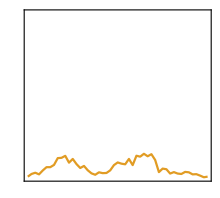

```mathematica
(* overlay the plots *)
fig5=Overlay[{fig5Chlorella,fig5Brach}]
```

### figure 6

```mathematica
fig6Chlorella=ListLinePlot[dataSet[[figureNums[[6]],;;,{1,2}]],
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],Style["Brachionus (females/ml)",White]},{"Time",""}},
Frame->{{True,False},{True,True}},
FrameTicks->{{None,None},{Range[0,100,20],None}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[1]]},
PlotRange->{{0,Max[dataSet[[figureNums[[6]],;;,1]]]},{0,5}},
Epilog->Text[Style["δ= "<>ToString[AccountingForm[deltaVals[[figureNums[[6]]]],{3,2}]],14],Scaled[labelPos]],
PlotRangeClipping->False,
AspectRatio->aRatio];
```

```mathematica
(* Plot of predator (brachionus) *)
fig6Brach=ListLinePlot[dataSet[[figureNums[[6]],;;,{1,3}]],
Joined->True,
LabelStyle->14,
FrameLabel->{{"",Style["Brachionus (females/ml)",White]},{"",""}},
Frame->{{False,True},{True,True}},
FrameTicks->{{None,None},{None,None}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[2]]},
PlotRange->{{0,Max[dataSet[[figureNums[[6]],;;,1]]]},{0,50}},
AspectRatio->aRatio];
```

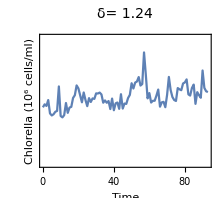
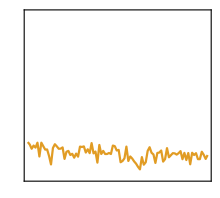

```mathematica
(* overlay the plots *)
fig6=Overlay[{fig6Chlorella,fig6Brach}]
```

### figure 7

```mathematica
fig7Chlorella=ListLinePlot[dataSet[[figureNums[[7]],;;,{1,2}]],
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],Style["Brachionus (females/ml)",White]},{"Time",""}},
Frame->{{True,False},{True,True}},
FrameTicks->{{None,None},{Range[0,100,20],None}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[1]]},
PlotRange->{{0,Max[dataSet[[figureNums[[7]],;;,1]]]},{0,5}},
Epilog->Text[Style["δ= "<>ToString[AccountingForm[deltaVals[[figureNums[[7]]]],{3,2}]],14],Scaled[labelPos]],
PlotRangeClipping->False,
AspectRatio->aRatio];
```

```mathematica
(* Plot of predator (brachionus) *)
fig7Brach=ListLinePlot[dataSet[[figureNums[[7]],;;,{1,3}]],
Joined->True,
LabelStyle->14,
FrameLabel->{{"",Style["Brachionus (females/ml)",TMBcolours[[2]]]},{"",""}},
Frame->{{False,True},{True,True}},
FrameTicks->{{None,Range[0,50,10]},{None,None}},
FrameStyle->{{Automatic,TMBcolours[[2]]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[2]]},
PlotRange->{{0,Max[dataSet[[figureNums[[7]],;;,1]]]},{0,50}},
AspectRatio->aRatio];
```

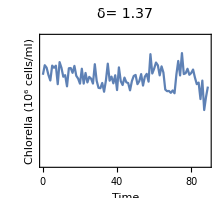
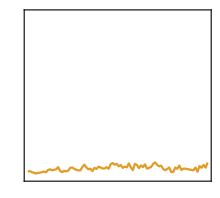

```mathematica
(* overlay the plots *)
fig7=Overlay[{fig7Chlorella,fig7Brach}]
```

## Power spectrum figures

We normalise the power spectrum plots so they are on the same scale for the figure - saves using many y axes - we are just showing qualitative features of spectrum, quantiitative feature given by Smax.

```mathematica
(* plot from -wmax to wmax *)
wmax=Pi;
(* y axis plot range *)
yRangeChlor={0,2};
yRangeBrach={0,2};
```

### Figure 1 PSD

```mathematica
imgpaddingPsd={{45,30},{40,20}};
imgSizePsd=190;
plotNormMax=2;

(* power spectrum data *)
psDataChlor=Transpose[psChlor[[figureNums[[1]]]]];
psDataBrach=Transpose[psBrach[[figureNums[[1]]]]];
```

```mathematica
(* compute smax for each pspec *)
smaxChlor=Max[psDataChlor[[;;,2]]];
smaxBrach=Max[psDataBrach[[;;,2]]];
```

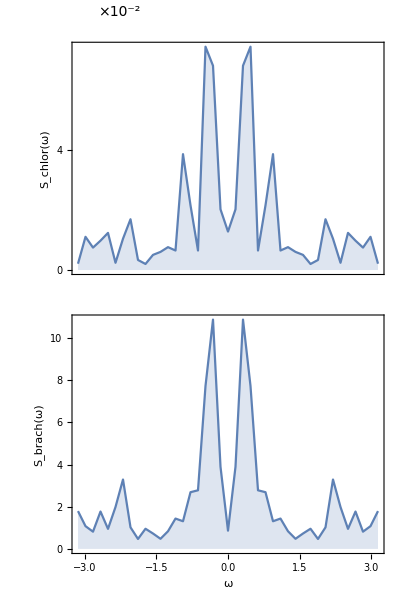

```mathematica
figPsd1=Grid[{{
ListLinePlot[psDataChlor,
PlotRange->{{-wmax,wmax},All},
Filling->Bottom,
Frame->True,
FrameLabel->{"","S_chlor(ω)"},
FrameTicks->{{{{0,0},{0.04,4},{0.08,8},{0.12,12}},None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
PlotRangeClipping->False,
Epilog->Text[Style["×10^-2",14],Scaled[{0.15,1.13}]]
]},
{ListLinePlot[psDataBrach,
PlotRange->{{-wmax,wmax},All},
Filling->Bottom,
Frame->True,
FrameLabel->{"ω","S_brach(ω)"},
LabelStyle->14,
ImageSize->imgSizePsd,
PlotRangeClipping->False,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7
]}}
,Spacings->{-2,-3}]
```

```mathematica
(* coherence factor *)
{coherFactorChlor,coherFactorBrach}={TBCoherFactor[Transpose[psDataChlor]],TBCoherFactor[Transpose[psDataBrach]]}
```

{0.111637,5.43852}

```mathematica
(* fold aic weights *)
{aicFoldChlor,aicFoldBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[1]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[1]]]}
```

{9.68379×10^-7,8.12188×10^-9}

```mathematica
(* hopf aic weights *)
{aicHopfChlor,aicHopfBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[2]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[2]]]}
```

{0.999999,1.}

```mathematica
(* normalise the data *)
dw=psDataChlor[[2,1]]-psDataChlor[[1,1]];
normChlor=Total[psDataChlor[[;;,2]]*dw];
psDataChlorNorm={psDataChlor[[;;,1]],psDataChlor[[;;,2]]/normChlor}//Transpose;
normBrach=Total[psDataBrach[[;;,2]]*dw];
psDataBrachNorm={psDataBrach[[;;,1]],psDataBrach[[;;,2]]/normBrach}//Transpose;
```

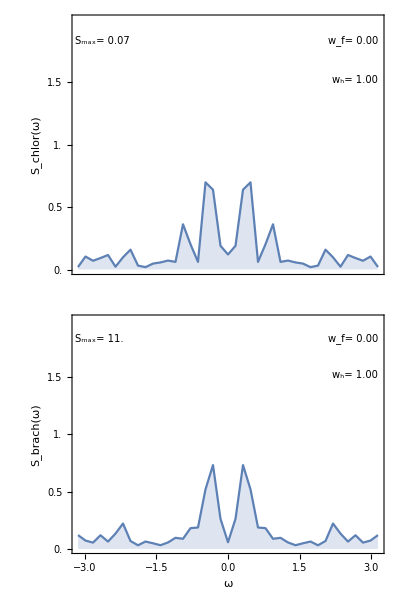

```mathematica
(* make plot for grid *)
figPsd1Norm=Grid[{{
ListLinePlot[psDataChlorNorm,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"","S_chlor(ω)"},
FrameTicks->{{Range[0,1.8,0.5],None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldChlor,{2,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfChlor,{2,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxChlor,{2,2}]],10],Scaled[{0.01,0.9}],Left]}
]},
{ListLinePlot[psDataBrachNorm,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameTicks->{{Range[0,1.8,0.5],None},{Automatic,None}},
FrameLabel->{"ω","S_brach(ω)"},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldBrach,{2,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfBrach,{2,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxBrach,{2,2}]],10],Scaled[{0.01,0.9}],Left]}
]}}
,Spacings->{-2,-3}]
```

### Figure 2 PSD

```mathematica
imgpaddingPsd={{45,30},{40,20}};
imgSizePsd=190;
plotNormMax=2;

(* power spectrum data *)
psDataChlor=Transpose[psChlor[[figureNums[[2]]]]];
psDataBrach=Transpose[psBrach[[figureNums[[2]]]]];
```

```mathematica
(* compute smax for each pspec *)
smaxChlor=Max[psDataChlor[[;;,2]]];
smaxBrach=Max[psDataBrach[[;;,2]]];
```

```mathematica
figPsd1=Grid[{{
ListLinePlot[psDataChlor,
PlotRange->{{-wmax,wmax},All},
Filling->Bottom,
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{None,None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
PlotRangeClipping->False,
Epilog->Text[Style["×10^-2",14],Scaled[{0.15,1.13}]]
]},
{ListLinePlot[psDataBrach,
PlotRange->{{-wmax,wmax},All},
Filling->Bottom,
Frame->True,
FrameLabel->{"ω",""},
LabelStyle->14,
ImageSize->imgSizePsd,
PlotRangeClipping->False,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7
]}}
,Spacings->{-2,-3}]
```

-Graphics-
-Graphics-

```mathematica
(* coherence factor *)
{coherFactorChlor,coherFactorBrach}={TBCoherFactor[Transpose[psDataChlor]],TBCoherFactor[Transpose[psDataBrach]]}
```

{0.0995435,237.439}

```mathematica
(* fold aic weights *)
{aicFoldChlor,aicFoldBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[1]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[1]]]}
```

{3.65665×10^-12,0.0000896393}

```mathematica
(* hopf aic weights *)
{aicHopfChlor,aicHopfBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[2]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[2]]]}
```

{1.,0.999662}

```mathematica
(* normalise the data *)
dw=psDataChlor[[2,1]]-psDataChlor[[1,1]];
normChlor=Total[psDataChlor[[;;,2]]*dw];
psDataChlorNorm={psDataChlor[[;;,1]],psDataChlor[[;;,2]]/normChlor}//Transpose;
normBrach=Total[psDataBrach[[;;,2]]*dw];
psDataBrachNorm={psDataBrach[[;;,1]],psDataBrach[[;;,2]]/normBrach}//Transpose;
```

```mathematica
(* make plot for grid *)
figPsd2Norm=Grid[{{
ListLinePlot[psDataChlorNorm,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{None,None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldChlor,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfChlor,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxChlor,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]},
{ListLinePlot[psDataBrachNorm,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameTicks->{{None,None},{Automatic,None}},
FrameLabel->{"ω",""},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldBrach,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfBrach,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxBrach,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]}}
,Spacings->{-2,-3}]
```

-Graphics-
-Graphics-

### Figure 3 PSD

```mathematica
imgpaddingPsd={{45,30},{40,20}};
imgSizePsd=190;
plotNormMax=2;

(* power spectrum data *)
psDataChlor=Transpose[psChlor[[figureNums[[3]]]]];
psDataBrach=Transpose[psBrach[[figureNums[[3]]]]];
```

```mathematica
(* compute smax for each pspec *)
smaxChlor=Max[psDataChlor[[;;,2]]];
smaxBrach=Max[psDataBrach[[;;,2]]];
```

```mathematica
figPsd1=Grid[{{
ListLinePlot[psDataChlor,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"","S_chlor(ω)"},
FrameTicks->{{{{0,0},{0.04,4},{0.08,8},{0.12,12}},None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
PlotRangeClipping->False,
Epilog->Text[Style["×10^-2",14],Scaled[{0.15,1.13}]]
]},
{ListLinePlot[psDataBrach,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameLabel->{"ω","S_brach(ω)"},
LabelStyle->14,
ImageSize->imgSizePsd,
PlotRangeClipping->False,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7
]}}
,Spacings->{-2,-3}]
```

-Graphics-
-Graphics-

```mathematica
(* coherence factor *)
{coherFactorChlor,coherFactorBrach}={TBCoherFactor[Transpose[psDataChlor]],TBCoherFactor[Transpose[psDataBrach]]}
```

{0.249383,26.7505}

```mathematica
(* fold aic weights *)
{aicFoldChlor,aicFoldBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[1]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[1]]]}
```

{1.,0.00378018}

```mathematica
(* hopf aic weights *)
{aicHopfChlor,aicHopfBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[2]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[2]]]}
```

{3.02571×10^-20,0.99622}

```mathematica
(* normalise the data *)
dw=psDataChlor[[2,1]]-psDataChlor[[1,1]];
normChlor=Total[psDataChlor[[;;,2]]*dw];
psDataChlorNorm={psDataChlor[[;;,1]],psDataChlor[[;;,2]]/normChlor}//Transpose;
normBrach=Total[psDataBrach[[;;,2]]*dw];
psDataBrachNorm={psDataBrach[[;;,1]],psDataBrach[[;;,2]]/normBrach}//Transpose;
```

```mathematica
(* make plot for grid *)
figPsd3Norm=Grid[{{
ListLinePlot[psDataChlorNorm,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{None,None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldChlor,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfChlor,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxChlor,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]},
{ListLinePlot[psDataBrachNorm,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameTicks->{{None,None},{Automatic,None}},
FrameLabel->{"ω",""},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldBrach,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfBrach,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxBrach,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]}}
,Spacings->{-2,-3}]
```

-Graphics-
-Graphics-

### Figure 4 PSD

```mathematica
imgpaddingPsd={{45,30},{40,20}};
imgSizePsd=190;
plotNormMax=2;

(* power spectrum data *)
psDataChlor=Transpose[psChlor[[figureNums[[4]]]]];
psDataBrach=Transpose[psBrach[[figureNums[[4]]]]];
```

```mathematica
(* compute smax for each pspec *)
smaxChlor=Max[psDataChlor[[;;,2]]];
smaxBrach=Max[psDataBrach[[;;,2]]];
```

```mathematica
figPsd1=Grid[{{
ListLinePlot[psDataChlor,
PlotRange->{{-wmax,wmax},All},
Filling->Bottom,
Frame->True,
FrameLabel->{"","S_chlor(ω)"},
FrameTicks->{{{{0,0},{0.04,4},{0.08,8},{0.12,12}},None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
PlotRangeClipping->False,
Epilog->Text[Style["×10^-2",14],Scaled[{0.15,1.13}]]
]},
{ListLinePlot[psDataBrach,
PlotRange->{{-wmax,wmax},All},
Filling->Bottom,
Frame->True,
FrameLabel->{"ω","S_brach(ω)"},
LabelStyle->14,
ImageSize->imgSizePsd,
PlotRangeClipping->False,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7
]}}
,Spacings->{-2,-3}]
```

-Graphics-
-Graphics-

```mathematica
(* coherence factor *)
{coherFactorChlor,coherFactorBrach}={TBCoherFactor[Transpose[psDataChlor]],TBCoherFactor[Transpose[psDataBrach]]}
```

{1.37688,15.2805}

```mathematica
(* fold aic weights *)
{aicFoldChlor,aicFoldBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[1]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[1]]]}
```

{1.44658×10^-28,0.828483}

```mathematica
(* hopf aic weights *)
{aicHopfChlor,aicHopfBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[2]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[2]]]}
```

{1.,0.0452806}

```mathematica
(* normalise the data *)
dw=psDataChlor[[2,1]]-psDataChlor[[1,1]];
normChlor=Total[psDataChlor[[;;,2]]*dw];
psDataChlorNorm={psDataChlor[[;;,1]],psDataChlor[[;;,2]]/normChlor}//Transpose;
normBrach=Total[psDataBrach[[;;,2]]*dw];
psDataBrachNorm={psDataBrach[[;;,1]],psDataBrach[[;;,2]]/normBrach}//Transpose;
```

```mathematica
(* make plot for grid *)
figPsd4Norm=Grid[{{
ListLinePlot[psDataChlorNorm,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{None,None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldChlor,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfChlor,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxChlor,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]},
{ListLinePlot[psDataBrachNorm,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameTicks->{{None,None},{Automatic,None}},
FrameLabel->{"ω",""},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldBrach,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfBrach,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxBrach,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]}}
,Spacings->{-2,-3}]
```

-Graphics-
-Graphics-

### Figure 5 PSD

```mathematica
imgpaddingPsd={{45,30},{40,20}};
imgSizePsd=190;
plotNormMax=2;

(* power spectrum data *)
psDataChlor=Transpose[psChlor[[figureNums[[5]]]]];
psDataBrach=Transpose[psBrach[[figureNums[[5]]]]];
```

```mathematica
(* compute smax for each pspec *)
smaxChlor=Max[psDataChlor[[;;,2]]];
smaxBrach=Max[psDataBrach[[;;,2]]];
```

```mathematica
figPsd1=Grid[{{
ListLinePlot[psDataChlor,
PlotRange->{{-wmax,wmax},All},
Filling->Bottom,
Frame->True,
FrameLabel->{"","S_chlor(ω)"},
FrameTicks->{{{{0,0},{0.04,4},{0.08,8},{0.12,12}},None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
PlotRangeClipping->False,
Epilog->Text[Style["×10^-2",14],Scaled[{0.15,1.13}]]
]},
{ListLinePlot[psDataBrach,
PlotRange->{{-wmax,wmax},All},
Filling->Bottom,
Frame->True,
FrameLabel->{"ω","S_brach(ω)"},
LabelStyle->14,
ImageSize->imgSizePsd,
PlotRangeClipping->False,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7
]}}
,Spacings->{-2,-3}]
```

-Graphics-
-Graphics-

```mathematica
(* coherence factor *)
{coherFactorChlor,coherFactorBrach}={TBCoherFactor[Transpose[psDataChlor]],TBCoherFactor[Transpose[psDataBrach]]}
```

{5.84339,45.0376}

```mathematica
(* fold aic weights *)
{aicFoldChlor,aicFoldBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[1]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[1]]]}
```

{2.51489×10^-26,2.05911×10^-46}

```mathematica
(* hopf aic weights *)
{aicHopfChlor,aicHopfBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[2]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[2]]]}
```

{1.,1.}

```mathematica
(* normalise the data *)
dw=psDataChlor[[2,1]]-psDataChlor[[1,1]];
normChlor=Total[psDataChlor[[;;,2]]*dw];
psDataChlorNorm={psDataChlor[[;;,1]],psDataChlor[[;;,2]]/normChlor}//Transpose;
normBrach=Total[psDataBrach[[;;,2]]*dw];
psDataBrachNorm={psDataBrach[[;;,1]],psDataBrach[[;;,2]]/normBrach}//Transpose;
```

```mathematica
(* make plot for grid *)
figPsd5Norm=Grid[{{
ListLinePlot[psDataChlorNorm,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{None,None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldChlor,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfChlor,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxChlor,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]},
{ListLinePlot[psDataBrachNorm,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameTicks->{{None,None},{Automatic,None}},
FrameLabel->{"ω",""},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldBrach,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfBrach,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxBrach,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]}}
,Spacings->{-2,-3}]
```

-Graphics-
-Graphics-

### Figure 6 PSD

```mathematica
imgpaddingPsd={{45,30},{40,20}};
imgSizePsd=190;
plotNormMax=2;

(* power spectrum data *)
psDataChlor=Transpose[psChlor[[figureNums[[6]]]]];
psDataBrach=Transpose[psBrach[[figureNums[[6]]]]];
```

```mathematica
(* compute smax for each pspec *)
smaxChlor=Max[psDataChlor[[;;,2]]];
smaxBrach=Max[psDataBrach[[;;,2]]];
```

```mathematica
figPsd1=Grid[{{
ListLinePlot[psDataChlor,
PlotRange->{{-wmax,wmax},All},
Filling->Bottom,
Frame->True,
FrameLabel->{"","S_chlor(ω)"},
FrameTicks->{{{{0,0},{0.04,4},{0.08,8},{0.12,12}},None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
PlotRangeClipping->False,
Epilog->Text[Style["×10^-2",14],Scaled[{0.15,1.13}]]
]},
{ListLinePlot[psDataBrach,
PlotRange->{{-wmax,wmax},All},
Filling->Bottom,
Frame->True,
FrameLabel->{"ω","S_brach(ω)"},
LabelStyle->14,
ImageSize->imgSizePsd,
PlotRangeClipping->False,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7
]}}
,Spacings->{-2,-3}]
```

-Graphics-
-Graphics-

```mathematica
(* coherence factor *)
{coherFactorChlor,coherFactorBrach}={TBCoherFactor[Transpose[psDataChlor]],TBCoherFactor[Transpose[psDataBrach]]}
```

{0.71902,4.83941}

```mathematica
(* fold aic weights *)
{aicFoldChlor,aicFoldBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[1]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[1]]]}
```

{0.0000657067,0.962141}

```mathematica
(* hopf aic weights *)
{aicHopfChlor,aicHopfBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[2]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[2]]]}
```

{0.999934,1.16572×10^-7}

```mathematica
(* normalise the data *)
dw=psDataChlor[[2,1]]-psDataChlor[[1,1]];
normChlor=Total[psDataChlor[[;;,2]]*dw];
psDataChlorNorm={psDataChlor[[;;,1]],psDataChlor[[;;,2]]/normChlor}//Transpose;
normBrach=Total[psDataBrach[[;;,2]]*dw];
psDataBrachNorm={psDataBrach[[;;,1]],psDataBrach[[;;,2]]/normBrach}//Transpose;
```

```mathematica
(* make plot for grid *)
figPsd6Norm=Grid[{{
ListLinePlot[psDataChlorNorm,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{None,None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldChlor,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfChlor,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxChlor,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]},
{ListLinePlot[psDataBrachNorm,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameTicks->{{None,None},{Automatic,None}},
FrameLabel->{"ω",""},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldBrach,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfBrach,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxBrach,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]}}
,Spacings->{-2,-3}]
```

-Graphics-
-Graphics-

### Figure 7 PSD

```mathematica
imgpaddingPsd={{45,30},{40,20}};
imgSizePsd=190;
plotNormMax=2;

(* power spectrum data *)
psDataChlor=Transpose[psChlor[[figureNums[[7]]]]];
psDataBrach=Transpose[psBrach[[figureNums[[7]]]]];
```

```mathematica
(* compute smax for each pspec *)
smaxChlor=Max[psDataChlor[[;;,2]]];
smaxBrach=Max[psDataBrach[[;;,2]]];
```

```mathematica
figPsd1=Grid[{{
ListLinePlot[psDataChlor,
PlotRange->{{-wmax,wmax},All},
Filling->Bottom,
Frame->True,
FrameLabel->{"","S_chlor(ω)"},
FrameTicks->{{{{0,0},{0.04,4},{0.08,8},{0.12,12}},None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
PlotRangeClipping->False,
Epilog->Text[Style["×10^-2",14],Scaled[{0.15,1.13}]]
]},
{ListLinePlot[psDataBrach,
PlotRange->{{-wmax,wmax},All},
Filling->Bottom,
Frame->True,
FrameLabel->{"ω","S_brach(ω)"},
LabelStyle->14,
ImageSize->imgSizePsd,
PlotRangeClipping->False,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7
]}}
,Spacings->{-2,-3}]
```

-Graphics-
-Graphics-

```mathematica
(* coherence factor *)
{coherFactorChlor,coherFactorBrach}={TBCoherFactor[Transpose[psDataChlor]],TBCoherFactor[Transpose[psDataBrach]]}
```

{0.169145,2.75333}

```mathematica
(* fold aic weights *)
{aicFoldChlor,aicFoldBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[1]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[1]]]}
```

{0.409649,0.883777}

```mathematica
(* hopf aic weights *)
{aicHopfChlor,aicHopfBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[2]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[2]]]}
```

{0.000040211,0.116046}

```mathematica
(* normalise the data *)
dw=psDataChlor[[2,1]]-psDataChlor[[1,1]];
normChlor=Total[psDataChlor[[;;,2]]*dw];
psDataChlorNorm={psDataChlor[[;;,1]],psDataChlor[[;;,2]]/normChlor}//Transpose;
normBrach=Total[psDataBrach[[;;,2]]*dw];
psDataBrachNorm={psDataBrach[[;;,1]],psDataBrach[[;;,2]]/normBrach}//Transpose;
```

```mathematica
(* make plot for grid *)
figPsd7Norm=Grid[{{
ListLinePlot[psDataChlorNorm,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{None,None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldChlor,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfChlor,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxChlor,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]},
{ListLinePlot[psDataBrachNorm,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameTicks->{{None,None},{Automatic,None}},
FrameLabel->{"ω",""},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldBrach,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfBrach,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxBrach,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]}}
,Spacings->{-2,-3}]
```

-Graphics-
-Graphics-

### Joint figure

```mathematica
gridFussmann=Grid[{{fig1,fig2,fig3,fig5,fig6,fig7},{figPsd1Norm,figPsd2Norm,figPsd3Norm,figPsd5Norm,figPsd6Norm,figPsd7Norm}},Spacings->{-6.5,0}]
```

-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-

```mathematica
(*Export["figures/empirical_ews_manu.png",gridFussmann,ImageResolution->200];*)
```